```mathematica
v="9";
p="0.1";
d="0.05";

gapp[10]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/v"<>v<>"-d"<>d<>"-l50k.txt",{Number,Number}];
ListPlot[gap]
```

ListPlot[gap]

```mathematica
ListAnimate[Table[ListPlot[gapp[x],PlotRange->{{0,40},{0,0.26}},PlotLabel->0.005+x*0.0005],{x,389}]]
```

```mathematica
gapmax={{0,0}};
gap0={{0,0}};
gapratio={{0,0}};
gapmax1={{0,0}};

For[i=0,i<390,i++,
d=0.005+i*0.0005;
dd=ToString[d];

gapp[i]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/Result/v"<>v<>"-d"<>dd<>"-l100k.txt",{Number,Number}];
gap0=Append[gap0,{d,gapp[i][[All,2]][[1]]}];
gapmax=Append[gapmax,{d,gapp[i][[All,2]][[10]]}];
gapmax1=Append[gapmax1,{d,gapp[i][[All,2]][[9]]}];
gapratio=Append[gapratio,{d,(gapp[i][[All,2]][[11]])/gapp[i][[All,2]][[10]]}];
]
gap0=Delete[gap0,1];
gapmax=Delete[gapmax,1];
gapmax1=Delete[gapmax1,1];
gapratio=Delete[gapratio,1];
```

```mathematica
gapp[20]
```

{{0,0},{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,2.13333×10^-6},{9,0.00140107},{10,0.0137757},{11,0.0151897},{12,0.0161473},{13,0.0160528},«99972»,{99986,0},{99987,0},{99988,0},{99989,0},{99990,0},{99991,0},{99992,0},{99993,0},{99994,0},{99995,0},{99996,0},{99997,0},{99998,0},{99999,0}}

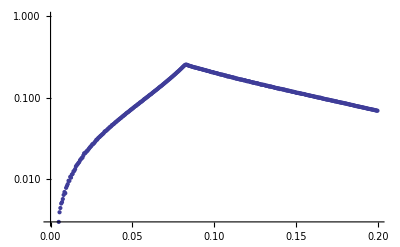

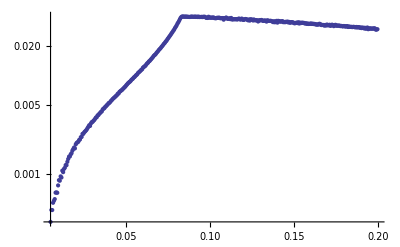

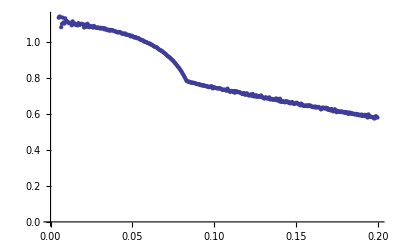

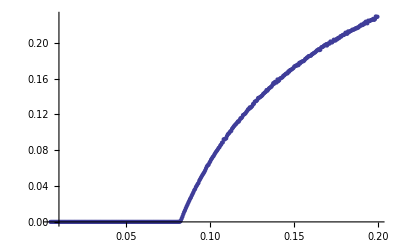

```mathematica
ListLogPlot[{gapmax}]
ListLogPlot[gapmax1,PlotRange->Full]
ListPlot[gapratio]
ListPlot[gap0,PlotRange->Full]
```

```mathematica
ListAnimate[Table[ListPlot[gapp[x],PlotRange->{{0,40},{0,0.26}},PlotLabel->0.005+x*0.0005],{x,389}]]
```